## First set

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
rawdata = Import["DataForPlotting\\Fig2C_data_1.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{66899,2}

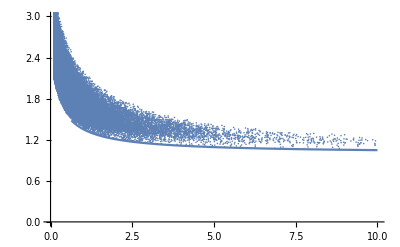

```mathematica
Show[ListPlot[rawdata,PlotRange->{{0,10},{0,3}}],Plot[Sqrt[1 + 1/(x*((1/(5*x))+1))],{x,0,10}]]
```

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.04}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2/10,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Max[rescaleddata[[;;,1]]]
```

1.98794

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.797274,1.3462}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,60000}];
```

```mathematica
Dimensions[densADJ]
```

{563,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]*10/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

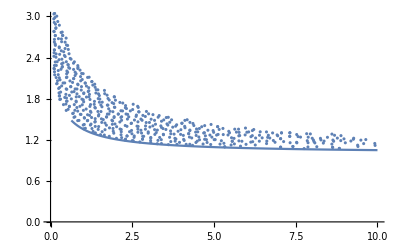

```mathematica
Show[ListPlot[densADJrescaled,PlotRange->{{0,10},{0,3}}],Plot[Sqrt[1 + 1/(x*((1/(5*x))+1))],{x,0,10}]]
```

```mathematica
Export["DataForPlotting\\Fig2C_densADJ_1.txt",densADJrescaled, "Table"]
```

## Second set

```mathematica
rawdata = Import["DataForPlotting\\Fig2C_data_2.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{244810,2}

```mathematica
Show[ListPlot[rawdata,PlotRange->{{0,10},{0,3}}],Plot[Sqrt[1 + 1/(x*((1/(1*x))+1))],{x,0,10}]]
```

-Graphics-

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.04}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2/10,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Max[rescaleddata[[;;,1]]]
```

1.99964

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.0533292,1.99034}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,30000}];
```

```mathematica
Dimensions[densADJ]
```

{527,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]*10/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

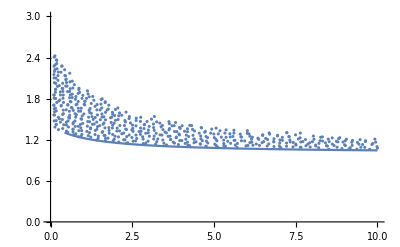

```mathematica
Show[ListPlot[densADJrescaled,PlotRange->{{0,10},{0,3}}],Plot[Sqrt[1 + 1/(x*((1/(1*x))+1))],{x,0,10}]]
```

```mathematica
Export["DataForPlotting\\Fig2C_densADJ_2.txt",densADJrescaled, "Table"]
```

## Third set

```mathematica
rawdata = Import["DataForPlotting\\Fig2C_data_3.txt","Table"];
```

```mathematica
Dimensions[rawdata]
```

{322970,2}

```mathematica
Show[ListPlot[rawdata,PlotRange->{{0,10},{0,3}}],Plot[Sqrt[1 + 1/(x*((1/(0.2*x))+1))],{x,0,10}]]
```

-Graphics-

```mathematica
theaddingfunction[x_,dat_]:=Module[{t=RandomSample[dat,1][[1]]},If[Length[Nearest[x,t,{Infinity,.04}]]<2,Prepend[x,t],x]]
```

```mathematica
rescaleddata = Table[{rawdata[[n]][[1]]*2/10,rawdata[[n]][[2]]},{n,1,Dimensions[rawdata][[1]]}];
```

```mathematica
Max[rescaleddata[[;;,1]]]
```

1.99994

```mathematica
Clear[densADJ];
densADJ=RandomSample[rescaleddata,1]
```

{{0.020276,1.21552}}

```mathematica
Do[densADJ=theaddingfunction[densADJ,rescaleddata],{n,1,30000}];
```

```mathematica
Dimensions[densADJ]
```

{326,2}

```mathematica
densADJrescaled = Table[{densADJ[[n]][[1]]*10/2,densADJ[[n]][[2]]},{n,1,Dimensions[densADJ][[1]]}];
```

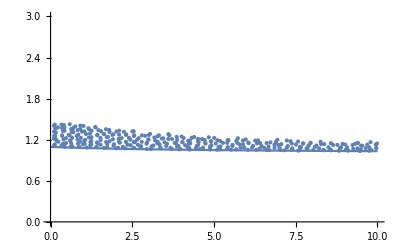

```mathematica
Show[ListPlot[densADJrescaled,PlotRange->{{0,10},{0,3}}],Plot[Sqrt[1 + 1/(x*((1/(0.2*x))+1))],{x,0,10}]]
```

```mathematica
Export["DataForPlotting\\Fig2C_densADJ_3.txt",densADJrescaled, "Table"]
```